Second moment of the gaussian distribution

Generujemy probke ze zmiennych x_i}i=1 do N
1. x0 dowolna wartosc poczatkowa
2. eta - ustaloana wartosc
propozycja:
x’ = x+ (2*r-1)*eta
(2r-1)*eta od -eta do eta
3.Akceptacja/Odrzucenie
rho[x0] prawdopodobienstwo starej wartosci x0
rho[x’] prawdopodobienstwo proponowanej wartosci

Exp[-alpha*x^2] = rho [x]
	rho[x’] > rho[x0] : dolaczamy x’ do probki
	rho[x’] < rho[x0]
		p = rho[x’]/rho[x0]
		akceptujemy x’ (x1=x’) z prawdopodobienstwem p
losujemy z roszkladu jednorodnego r nalezace do [0,1]
r<p -> x1=x’
r>p -> 
	1.Odrzucamy 
	2.x1 = x0

```mathematica
Initial Values;
n = 1;
alpha = 2;
M = 100;
eta = 1.5
LimitInt = 2
```

1.5

2

9652429566*^9, 
   3.657819701272854*^9}, {3.657820564963727*^9, 3.657820565414349*^9}, {
   3.657820727431361*^9, 3.657820736307144*^9}, {3.6578209723562727`*^9,

```mathematica
calculated Funct :
```

```mathematica
Fun[x_] = x^2;
```

```mathematica
Average of Fun:
```

```mathematica
Average = Integrate[Fun[x]*Exp[-alpha*x^2],{x,-Infinity,Infinity}]/Integrate[Exp[-alpha*x^2],{x,-Infinity,Infinity}]
```

1/4

```mathematica
Single value probabillity:
```

```mathematica
SingleCoordinateValueProb[x_] :=x^4* Exp[-alpha*x^2]
```

```mathematica
InitialPath = RandomReal[{-LimitInt,LimitInt},n];
termalizacja = {}
cnt =0
 - akceptancja w funkcji eta
```

{}

0

-1.5 akceptancja funkcji w

{}

```mathematica
etaacceptance = {};
Do[
PathNew = InitialPath;
PathOld = InitialPath;
Trajectories ={};
cnt= 0;
cnt1 = 0;
Do[
	(* generate sweep *)
	Do[
		FindNewCoordinateProposition = (RandomInteger[n-1]+1);
		r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];
		Part[PathNew,FindNewCoordinateProposition] =  Part[PathOld,FindNewCoordinateProposition] + (2*r-1)*eta;
		RhoXPrime = SingleCoordinateValueProb[Part[PathNew,FindNewCoordinateProposition]];
		RhoX =  SingleCoordinateValueProb[Part[PathOld,FindNewCoordinateProposition]];
		If[RhoXPrime>RhoX,
			cnt++;
			Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ;
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]];,
			If[RandomReal[]<(RhoXPrime/RhoX),
			cnt++;
			Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ;
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]];,
			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 
			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)
			]
		]
		(*	Print[Part[PathOld,FindNewCoordinateProposition]];
			Print[FindNewCoordinateProposition];*)
		,{n}
	];
cnt1++;
AppendTo[termalizacja,{RhoX,cnt}];
If[cnt1==M,AppendTo[etaacceptance,{eta,cnt/M}];(*Print[eta,cnt/M]*)
,
];
,{M}];
,{eta,Range[0,12,0.1]}]
```

```mathematica
ListPlot[{termalizacja}]
```

```mathematica
etaacceptance2 = etaacceptance;
```

```mathematica
etaacceptance1 = etaacceptance;
```

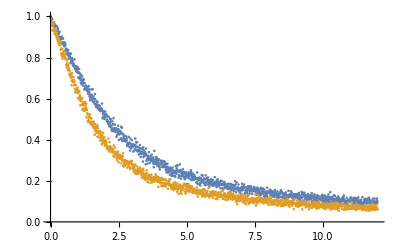

```mathematica
ListPlot[{etaacceptance1,etaacceptance2}]
```

```mathematica
Sigma 1/2
```

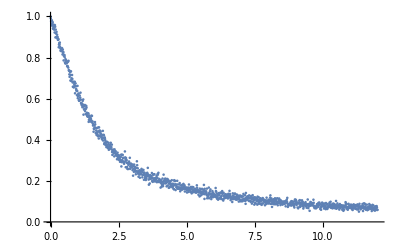

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
Termalizacja Liczba sweepow 10000, eta od 0 do 20 z krokiem 0.01
```

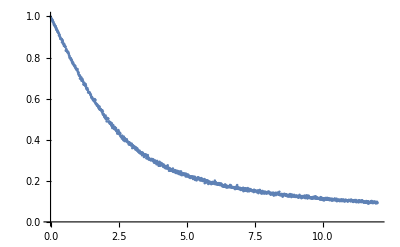

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
Termalizacja Liczba sweepow 1000, eta od 0 do 20 z krokiem 0.01
```

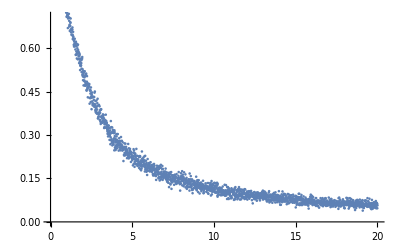

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
Termalizacja Liczba sweepow 100, eta od 0 do 20 z krokiem 0.01
```

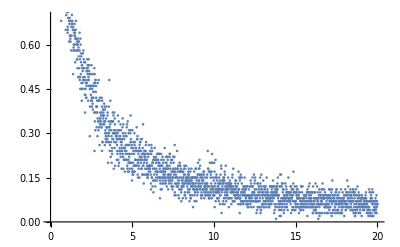

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
Termalizacja Liczba sweepow 10, eta od 0 do 20 z krokiem 0.01
```

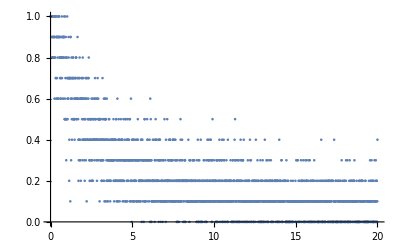

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
Termalizacja Liczba sweepow 100, eta od 0 do 20 z krokiem 0.1
```

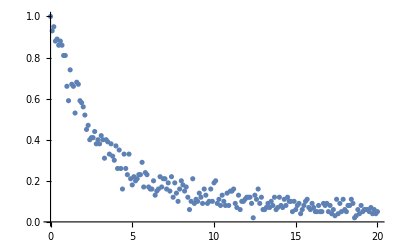

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
Termalizacja Liczba sweepow 1000, eta od 0 do 20 z krokiem 0.1
```

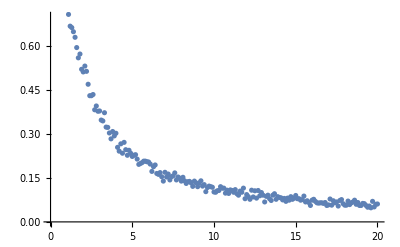

```mathematica
ListPlot[{etaacceptance}]
```

Badanie zbieżności :

```mathematica
SingleCoordinateValueProb[x_] :=x^4* Exp[-alpha*x^2]
```

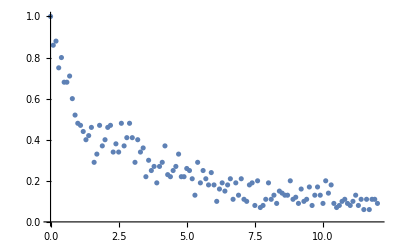

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
SingleCoordinateValueProb[x_] :=x^2* Exp[-alpha*x^2]
```

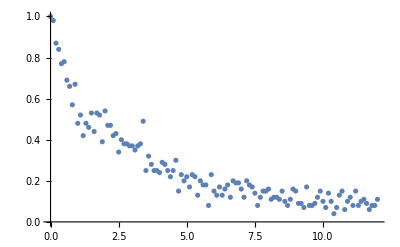

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
cos[x]
```

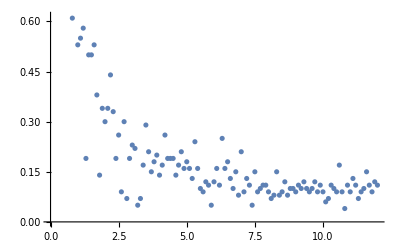

```mathematica
ListPlot[{etaacceptance}]
```

```mathematica
SingleCoordinateValueProb[x_] :=Cos[x]* Exp[-alpha*x^2]
```

```mathematica
M=100
InitialPath = {12}
termalizacja= {}
eta = 8
PathNew = InitialPath;
PathOld = InitialPath;
testnakonwergentnosc = {};
Do[

Trajectories ={};
	(* generate sweep *)
	Do[
		FindNewCoordinateProposition = (RandomInteger[n-1]+1);
		r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];
		Part[PathNew,FindNewCoordinateProposition] =  Part[PathOld,FindNewCoordinateProposition] + (2*r-1)*eta;
		RhoXPrime = SingleCoordinateValueProb[Part[PathNew,FindNewCoordinateProposition]];
		RhoX =  SingleCoordinateValueProb[Part[PathOld,FindNewCoordinateProposition]];
		If[RhoXPrime>RhoX,
			cnt++;
			Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ;
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]];
			AppendTo[testnakonwergentnosc, Part[PathOld,FindNewCoordinateProposition]*FindNewCoordinateProposition];
			AppendTo[termalizacja, Part[PathOld,FindNewCoordinateProposition]*RhoXPrime];,
			If[RandomReal[]<(RhoXPrime/RhoX),
			cnt++;
			Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ;
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]];
			AppendTo[testnakonwergentnosc, Part[PathOld,FindNewCoordinateProposition]*FindNewCoordinateProposition];
			AppendTo[termalizacja, Part[PathOld,FindNewCoordinateProposition]*RhoXPrime];,
AppendTo[termalizacja, Part[PathOld,FindNewCoordinateProposition]*RhoXPrime];
			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 
			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)
			]
		]
		(*	Print[Part[PathOld,FindNewCoordinateProposition]];
			Print[FindNewCoordinateProposition];*)
		,{n}
	];

,{M}];
```

100

{12}

{}

8

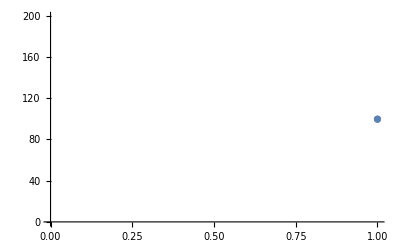

```mathematica
ListPlot[testnakonwergentnosc[[Range[1,1]]]]
```

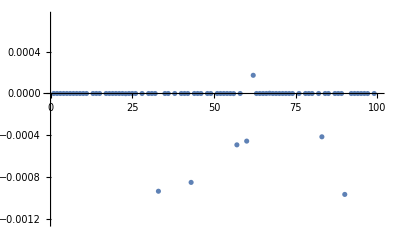

x^4

```mathematica
ListPlot[termalizacja]
x^4
```

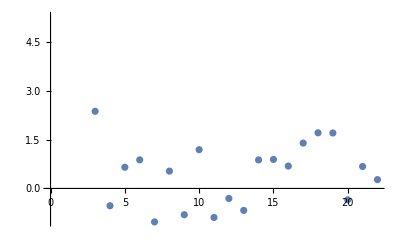

x^2

```mathematica
ListPlot[testnakonwergentnosc]
x^2
```

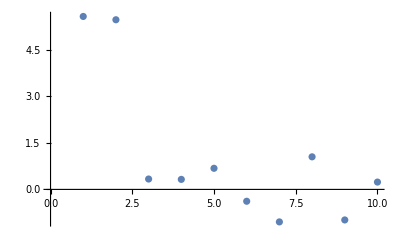

cos[x]

```mathematica
ListPlot[testnakonwergentnosc]
cos[x]
```

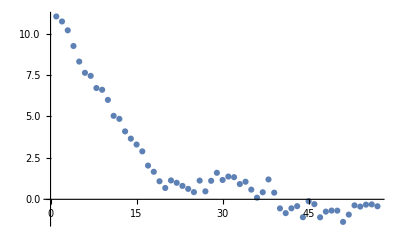

```mathematica
ListPlot[testnakonwergentnosc]
x
```

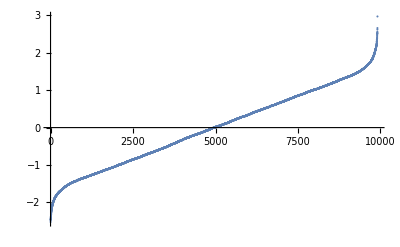

```mathematica
ListPlot[Sort[testnakonwergentnosc]]
```

```mathematica
testnakonwergentnosc[[Range[1,100]]]
```

{0.119344,0.990766,1.21734,-0.840571,0.199404,-0.398639,-1.83375,-0.831475,0.967474,1.10526,0.864045,1.62418,-0.453654,1.39491,1.12607,0.890268,1.11562,-0.373307,-0.167311,0.935155,-0.335877,0.433299,1.28306,-1.14809,1.3515,1.41825,-1.51785,0.986704,-1.83672,-0.852526,1.10514,-0.735114,1.43271,1.12849,1.31859,-0.0780258,0.662182,0.425471,0.193799,-0.295391,-0.328367,-1.17999,-0.146423,0.133241,0.500486,-1.51937,0.67129,1.25984,1.13237,0.811534,-0.817945,1.64867,-0.711545,-0.524749,-0.511607,-1.67935,1.85959,2.52076,0.88777,0.362129,0.491681,-1.44838,-0.605514,0.300931,0.600583,-0.00460653,-1.28368,-0.447079,0.922582,-0.5926,1.54348,-1.31559,0.204955,0.867669,-0.172258,-1.39367,0.124056,-1.89551,0.371378,0.696925,0.556767,1.18697,0.602289,0.188963,-0.190879,-0.941873,0.860599,1.26293,-1.57767,0.392492,-0.247623,0.188614,0.125559,1.87878,-0.486854,0.258556,-2.33335,-1.33734,-0.83492,0.867}

```mathematica
Rysowanie dla zadanego eta
```

```mathematica
eta =0.0000001;
PathNew = InitialPath;
PathOld = InitialPath;
Trajectories ={};
Do[
	(* generate sweep *)
	Do[
		FindNewCoordinateProposition = (RandomInteger[n-1]+1);
		r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];
		Part[PathNew,FindNewCoordinateProposition] =  Part[PathOld,FindNewCoordinateProposition] + (2*r-1)*eta;
		RhoXPrime = SingleCoordinateValueProb[Part[PathNew,FindNewCoordinateProposition]];
		RhoX =  SingleCoordinateValueProb[Part[PathOld,FindNewCoordinateProposition]];
		If[RhoXPrime>RhoX,
			Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ;
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]];,
			If[RandomReal[]<(RhoXPrime/RhoX),
			Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ;
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]];,
			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 
			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];
			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)
			]
		]
		(*	Print[Part[PathOld,FindNewCoordinateProposition]];
			Print[FindNewCoordinateProposition];*)
		,{n}
	]
,{M}]
```

```mathematica
Sweepes - 50000
```

```mathematica
Eta = 0.0000001
```

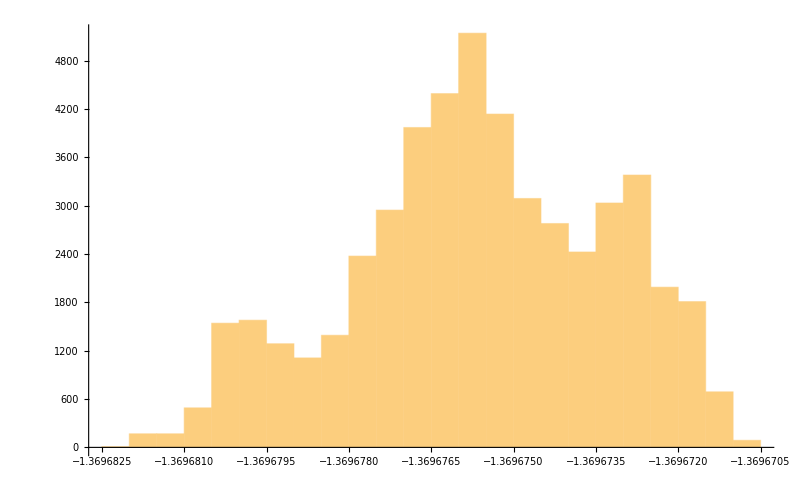

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 0.00001
```

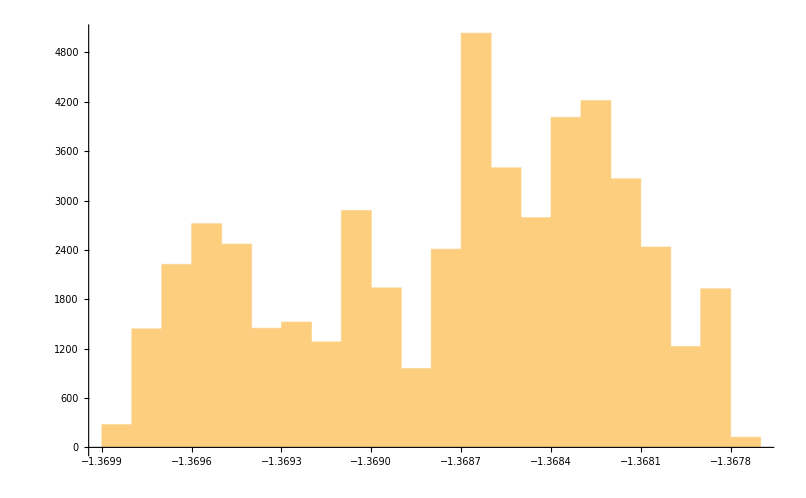

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 0.0001
```

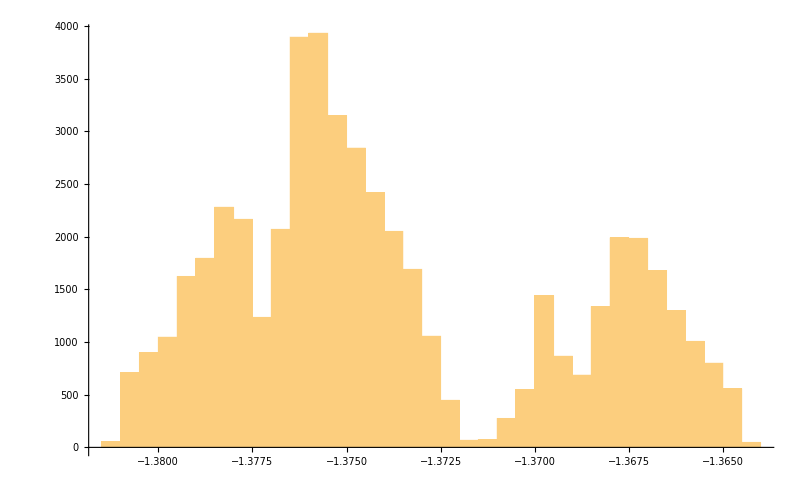

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 0.001
```

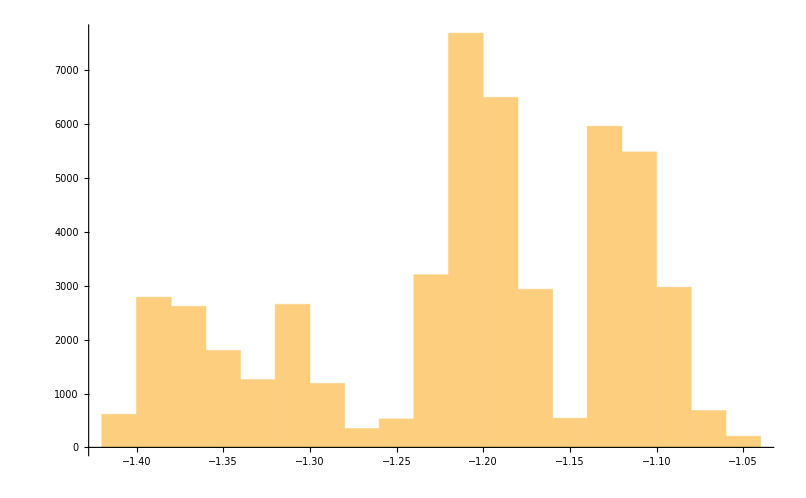

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 0.01
```

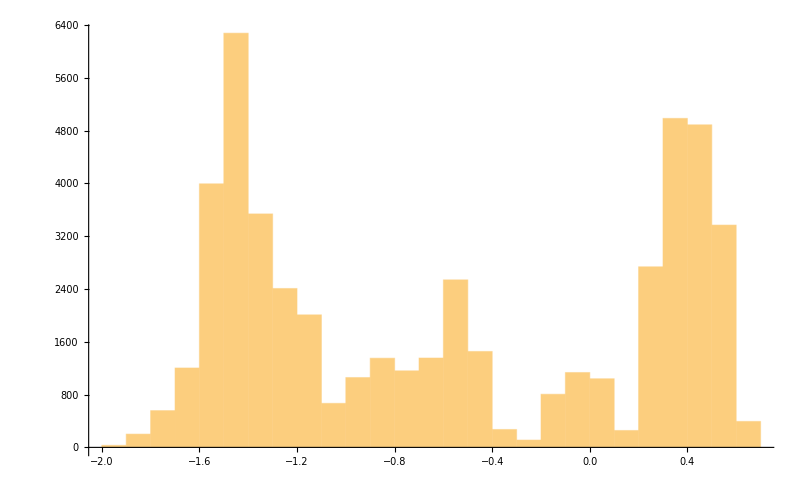

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 0.1
```

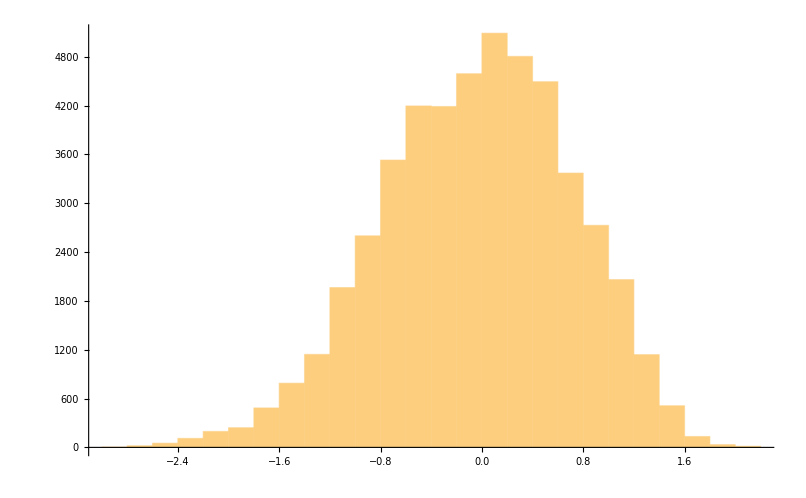

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 1
```

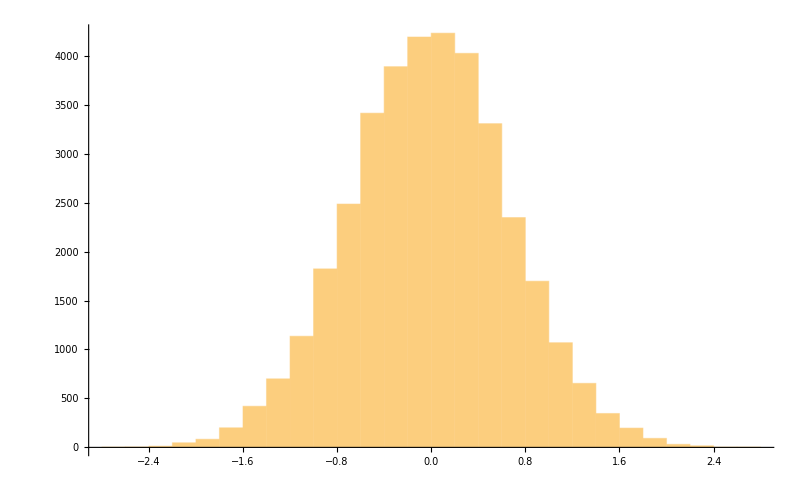

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 8.5
```

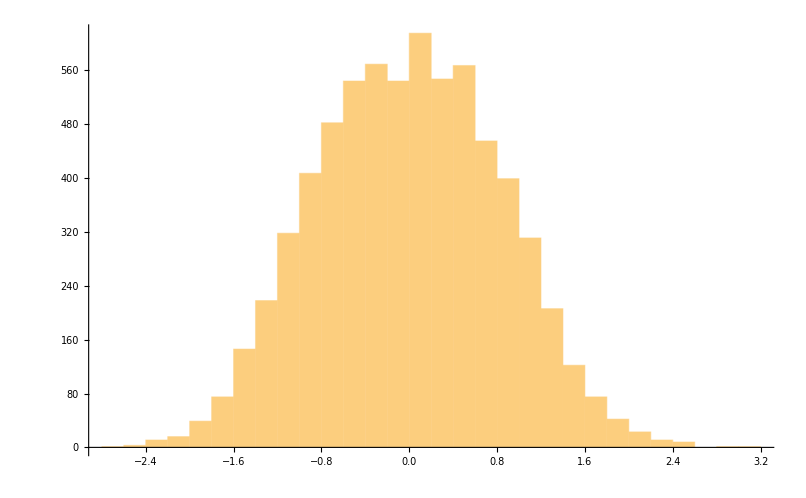

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 20
```

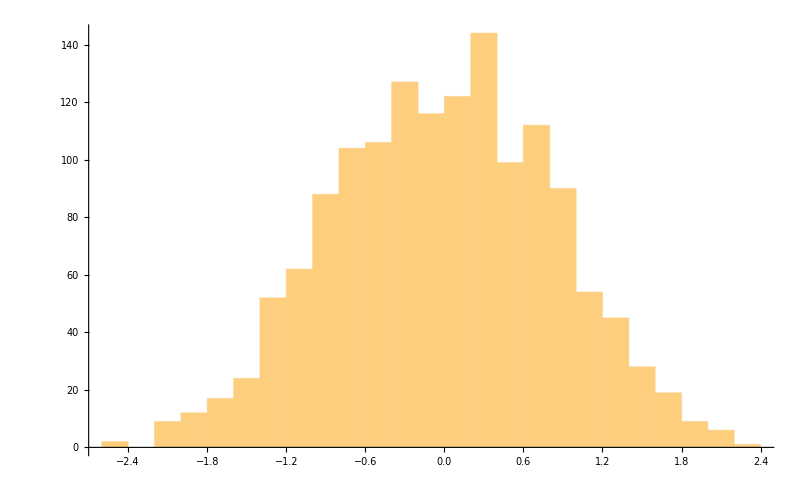

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
.16.16.1a
```

```mathematica
Eta = 40
```

```mathematica
Show[Histogram[Trajectories]]
```

-Graphics-

```mathematica
Eta = 100
```

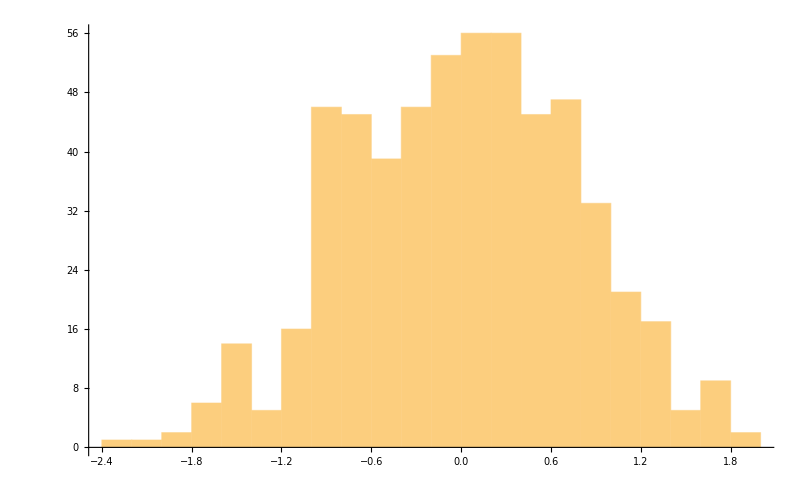

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 200
```

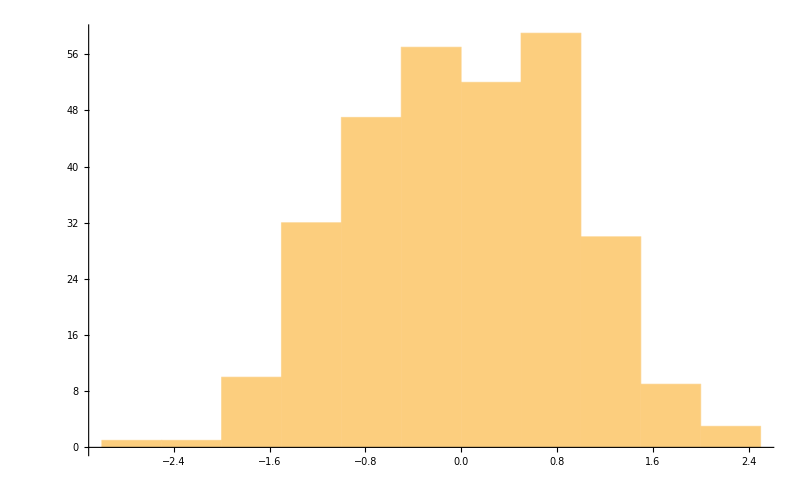

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 500
```

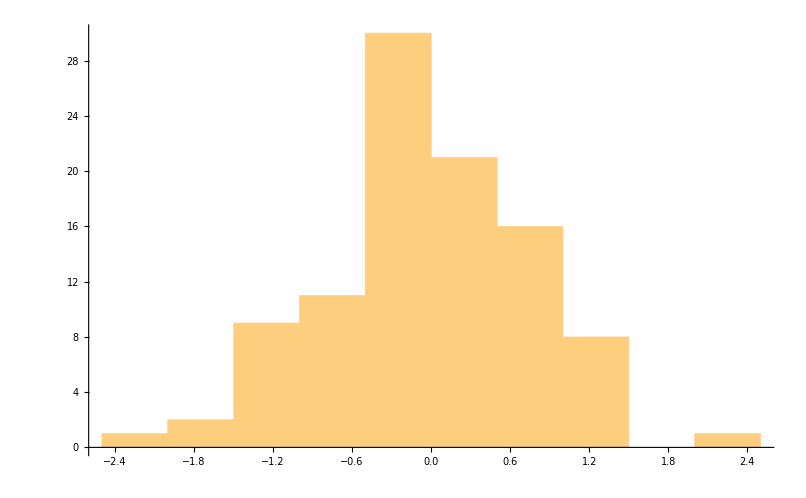

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 1000
```

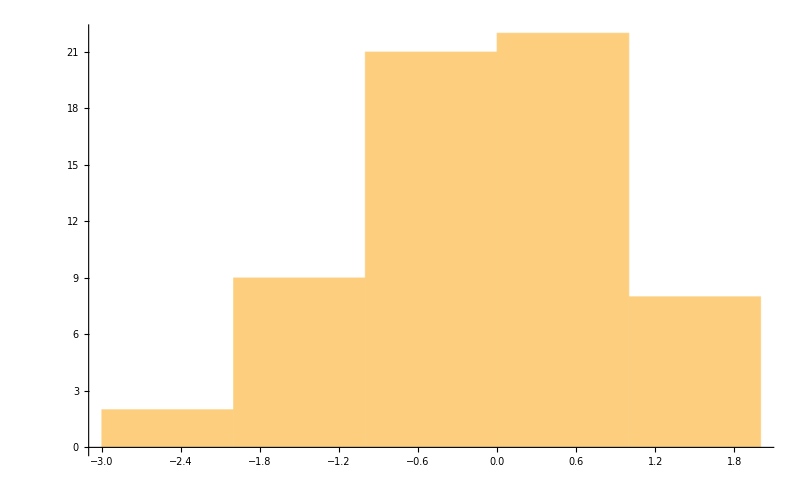

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 5000
```

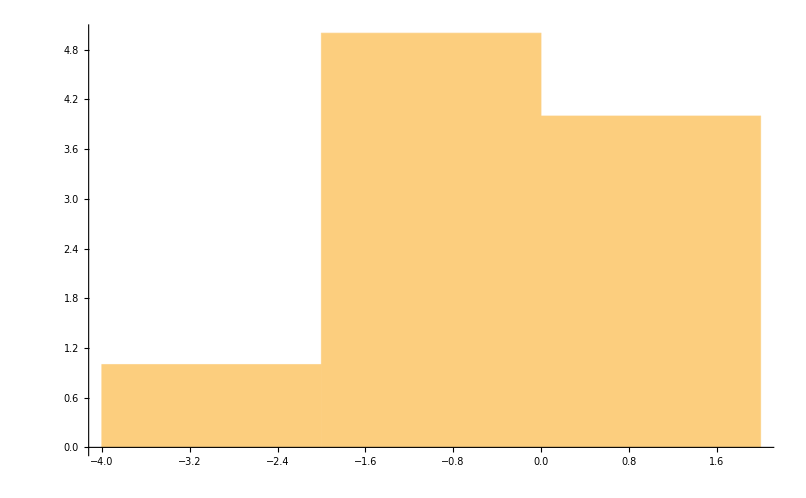

```mathematica
Show[Histogram[Trajectories]]
```

```mathematica
Eta = 50000
```

```mathematica
Show[Histogram[Trajectories]]
```

-Graphics-

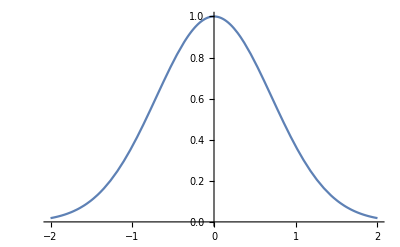

```mathematica
Plot[SingleCoordinateValueProb[x],{x,-2,2}]
```

```mathematica
n = 1000;
eta = 1/10;
alpha = 1;
LimitInt = 2
```

2

j+WyOrDUDVZ/6pjv1IBkOd+rpnjJnoOnNj0LDr5NBjWI5K2zMQMyZ
NSULMckQZPDyxOFLDFSi1XzZ4kcyCNPqY5kUGUhwgtHjdCoFTE0uB7XvYSBl
E2JvKDEFKrbfenSvmo7GniIXjbg0aB8zGdgop6OMrCWehYo0GC/

```mathematica
InitialPath = RandomReal[{-LimitInt,LimitInt},n];
PathNew = InitialPath;
PathOld = InitialPath;
```

```mathematica
Do[
	FindNewCoordinateProposition = 1;(*(RandomInteger[n-1]+1);*)
	r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];
	Part[PathNew,FindNewCoordinateProposition] =  Part[PathOld,FindNewCoordinateProposition] + (2*r-1)*eta;
	RhoXPrime = SingleCoordinateValueProb[Part[PathNew,FindNewCoordinateProposition]];
	RhoX =  SingleCoordinateValueProb[Part[PathOld,FindNewCoordinateProposition]];
	If[RhoXPrime>RhoX,
		Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ,
		If[RandomReal[]<(RhoXPrime/RhoX),
		Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ,
		(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 
		Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition] 
		]
	]
	,{n}
]
```

Plot::plln: Limiting value Null in {x, Null, Null} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[Directive[EdgeForm[Directive[Thickness[Skeleton[1]], Opacity[Skeleton[1]]]], RGBColor[0.987148`, 0.8073604000000001`, 0.49470040000000004`]], List[List[], List[Directive[EdgeForm[Skeleton[1]], RGBColor[Skeleton[3]]], List[List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]], List[Skeleton[1]]]], List[], List[]]], List[List[], List[], List[], List[], List[], List[], List[], List[], List[], List[], List[], List[]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[-1.048`, 0]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[PlotRange, List[List[-1.`, 1.4`], List[All, All]]], Rule[PlotRangePadding, List[List[Scaled[0.02`], Scaled[0.02`]], List[Scaled[0.02`], Scaled[0.05`]]]], Rule[Ticks, List[Automatic, Automatic]]]], Plot[Exp[-alpha x^2], {x, Null, Null}].

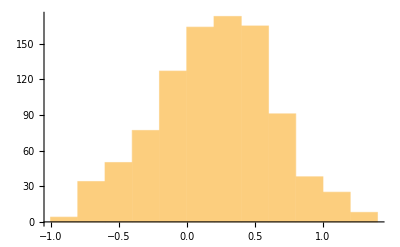
Show[-Graphics-,Plot[Exp[-alpha x^2],{x,Null,Null}]]

Piecewise

```mathematica
Show[Histogram[Trajectories],
Plot[Exp[-alpha*x^2],{x,,}]]
Piecewise
```

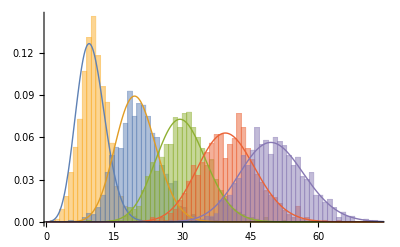

```mathematica
Show[Histogram[Table[RandomInteger[PoissonDistribution[10 i],1000],{i,5}],{1},"PDF",PlotRange->All],Plot[Evaluate[Table[PDF[PoissonDistribution[10 μ],x],{μ,5}]],{x,0,80},PlotStyle->Thick,PlotRange->All]]
```